```mathematica
ClearAll[data]
```

```mathematica
l=8;

Do[
ll=ToString[l];
data[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-mod.txt",{Number,Number,Number,Number}];
m2[l]=Table[{data[l][[All,1]][[i]],Abs[data[l][[All,2]][[i]]]},{i,1,Length[data[l]]}];
χ2[l]=Table[{data[l][[All,1]][[i]],data[l][[All,1]][[i]]*l^3*(data[l][[All,3]][[i]]-data[l][[All,2]][[i]]*data[l][[All,2]][[i]])},{i,1,Length[data[l]]}];
,{l,{8,16,32,48,64}}]
data[64]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/l64.txt",{Number,Number,Number,Number}];
```

```mathematica
(*Do[
ll=ToString[l];
data[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>".txt",{Number,Number,Number,Number}];
m[l]=Table[{data[l][[All,1]][[i]],Abs[data[l][[All,2]][[i]]]},{i,1,Length[data[l]]}];
χ[l]=Table[{data[l][[All,1]][[i]],data[l][[All,3]][[i]]-data[l][[All,2]][[i]]*data[l][[All,2]][[i]]},{i,1,Length[data[l]]}];
,{l,{8,16,32}}]*)
```

64

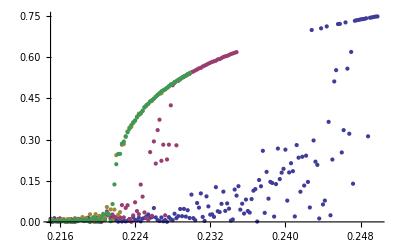

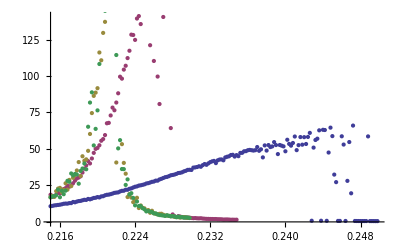

```mathematica
l=64
ListPlot[{m[8],m[16],m[32],m[48]},PlotRange->Full]
ListPlot[{χ[8],χ[16],χ[32],χ[48]}]
```

```mathematica
Do[
ll=ToString[l];
data[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-new1.txt",{Number,Number,Number,Number}];
m2[l]=Table[{data[l][[All,1]][[i]],Abs[data[l][[All,2]][[i]]]},{i,1,Length[data[l]]}];
χ2[l]=Table[{data[l][[All,1]][[i]],data[l][[All,1]][[i]]*l^3*(data[l][[All,3]][[i]]-data[l][[All,2]][[i]]*data[l][[All,2]][[i]])},{i,1,Length[data[l]]}];
,{l,{8,16,32}}]
```

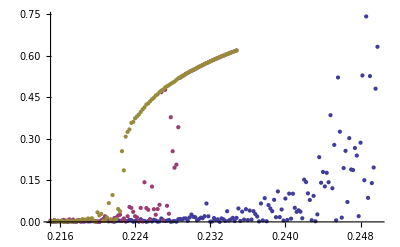

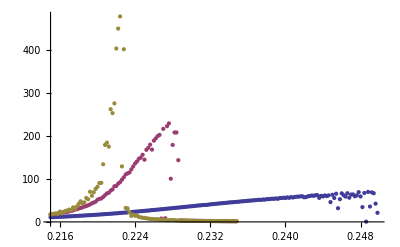

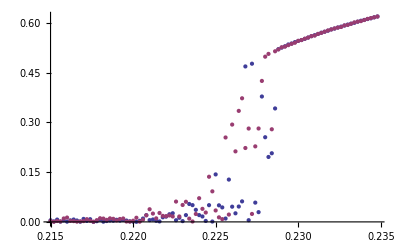

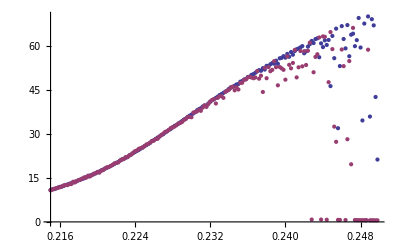

```mathematica
ListPlot[{m2[8],m2[16],m2[32]},PlotRange->Full]
ListPlot[{χ2[8],χ2[16],χ2[32]},PlotRange->Full]
ListPlot[{m2[16],m[16]},PlotRange->Full]
ListPlot[{χ2[8],χ[8]}]
```

```mathematica
Do[
ll=ToString[l];
data[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run1.txt",{Number,Number,Number,Number}];
m2[l]=Table[{data[l][[All,1]][[i]],Abs[data[l][[All,2]][[i]]]},{i,1,Length[data[l]]}];
χ2[l]=Table[{data[l][[All,1]][[i]],data[l][[All,1]][[i]]*l^3*(data[l][[All,3]][[i]]-data[l][[All,2]][[i]]*data[l][[All,2]][[i]])},{i,1,Length[data[l]]}];
,{l,{8,16,32,48}}]
```

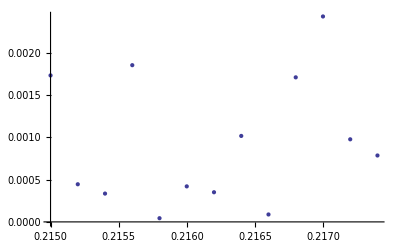

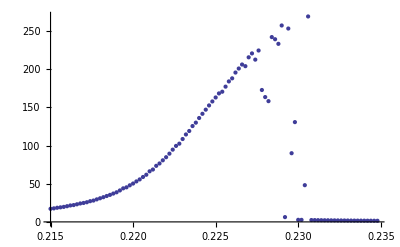

```mathematica
ListPlot[m2[48]]
ListPlot[χ2[16]]
```

```mathematica
l=8;
ll=ToString[l];
data1[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run1.txt",{Number,Number,Number,Number}];
data2[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run2.txt",{Number,Number,Number,Number}];
data[l]=Table[{data1[l][[All,1]][[i]],(Abs[data1[l][[All,2]][[i]]]+Abs[data2[l][[All,2]][[i]]])/2.,(data1[l][[All,3]][[i]]+data2[l][[All,3]][[i]])/2.,(data1[l][[All,4]][[i]]+data2[l][[All,4]][[i]])/2.},{i,1,Length[data1[l]]}];
```

```mathematica
l=32;
ll=ToString[l];
data1[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run1.txt",{Number,Number,Number,Number}];
data2[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run2.txt",{Number,Number,Number,Number}];
data3[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run3.txt",{Number,Number,Number,Number}];
data4[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run4.txt",{Number,Number,Number,Number}];
dataaux1[l]=Table[{data1[l][[All,1]][[i]],(Abs[data1[l][[All,2]][[i]]]+Abs[data2[l][[All,2]][[i]]]+Abs[data3[l][[All,2]][[i]]]+Abs[data4[l][[All,2]][[i]]])/4.,(data1[l][[All,3]][[i]]+data2[l][[All,3]][[i]]+data3[l][[All,3]][[i]]+data4[l][[All,3]][[i]])/4.,(data1[l][[All,4]][[i]]+data2[l][[All,4]][[i]]+data3[l][[All,4]][[i]]+data4[l][[All,4]][[i]])/4.},{i,1,Length[data1[l]]}];

(*data5[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run5.txt",{Number,Number,Number,Number}];
data6[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run6.txt",{Number,Number,Number,Number}];
data7[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run7.txt",{Number,Number,Number,Number}];
data8[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run8.txt",{Number,Number,Number,Number}];
dataaux2[l]=Table[{data5[l][[All,1]][[i]],(Abs[data5[l][[All,2]][[i]]]+Abs[data6[l][[All,2]][[i]]]+Abs[data7[l][[All,2]][[i]]]+Abs[data8[l][[All,2]][[i]]])/4.,(data5[l][[All,3]][[i]]+data6[l][[All,3]][[i]]+data7[l][[All,3]][[i]]+data8[l][[All,3]][[i]])/4.,(data5[l][[All,4]][[i]]+data6[l][[All,4]][[i]]+data7[l][[All,4]][[i]]+data8[l][[All,4]][[i]])/4.},{i,1,Length[data5[l]]}];
data[l]=Join[dataaux1[l],dataaux2[l]];

data[l]=Sort[data[l],#1[[1]]<#2[[1]]&];*)

data[l]=dataaux1[l];
```

```mathematica
l=48;
ll=ToString[l];
data1[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run1.txt",{Number,Number,Number,Number}];
data2[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run2.txt",{Number,Number,Number,Number}];
data3[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run3.txt",{Number,Number,Number,Number}];
data4[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run4.txt",{Number,Number,Number,Number}];
data5[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run5.txt",{Number,Number,Number,Number}];
data6[l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-l"<>ll<>"-run6.txt",{Number,Number,Number,Number}];
data[l]=Table[{data1[l][[All,1]][[i]],(Abs[data1[l][[All,2]][[i]]]+Abs[data2[l][[All,2]][[i]]]+Abs[data3[l][[All,2]][[i]]]+Abs[data4[l][[All,2]][[i]]]+Abs[data5[l][[All,2]][[i]]]+Abs[data6[l][[All,2]][[i]]])/6.,(data1[l][[All,3]][[i]]+data2[l][[All,3]][[i]]+data3[l][[All,3]][[i]]+data4[l][[All,3]][[i]]+data5[l][[All,3]][[i]]+data6[l][[All,3]][[i]])/6.,(data1[l][[All,4]][[i]]+data2[l][[All,4]][[i]]+data3[l][[All,4]][[i]]+data4[l][[All,4]][[i]]+data5[l][[All,4]][[i]]+data6[l][[All,4]][[i]])/6.},{i,1,Length[data1[l]]}];
```

```mathematica
Do[
ll=ToString[l];
m[l]=Table[{data[l][[All,1]][[i]],Abs[data[l][[All,2]][[i]]]},{i,1,Length[data[l]]}];
χ[l]=Table[{data[l][[All,1]][[i]],data[l][[All,1]][[i]]*l^3*(data[l][[All,3]][[i]]-data[l][[All,2]][[i]]*data[l][[All,2]][[i]])},{i,1,Length[data[l]]}];

χmod[l]=Table[{χ[l][[All,1]][[i]],(χ[l][[All,2]][[i-5]]+χ[l][[All,2]][[i-4]]+χ[l][[All,2]][[i-3]]+χ[l][[All,2]][[i-2]]+χ[l][[All,2]][[i-1]]+χ[l][[All,2]][[i]]+χ[l][[All,2]][[i+1]]+χ[l][[All,2]][[i+2]]+χ[l][[All,2]][[i+3]]+χ[l][[All,2]][[i+4]]+χ[l][[All,2]][[i+5]])/11.0},{i,6,Length[χ[l]]-10}];

mmod[l]=Table[{m[l][[All,1]][[i]],(m[l][[All,2]][[i-5]]+m[l][[All,2]][[i-4]]+m[l][[All,2]][[i-3]]+m[l][[All,2]][[i-2]]+m[l][[All,2]][[i-1]]+m[l][[All,2]][[i]]+m[l][[All,2]][[i+1]]+m[l][[All,2]][[i+2]]+m[l][[All,2]][[i+3]]+m[l][[All,2]][[i+4]]+m[l][[All,2]][[i+5]])/11.0},{i,6,Length[m[l]]-10}];


iχ[l]=Interpolation[χ[l]];
iχmod[l]=Interpolation[χmod[l]];

pic[l]=Plot[{iχmod[l][x]},{x,χmod[l][[All,1]][[1]],χmod[l][[All,1]][[Length[χmod[l]]]]}];

,{l,{8,16,32,48}}]
```

8

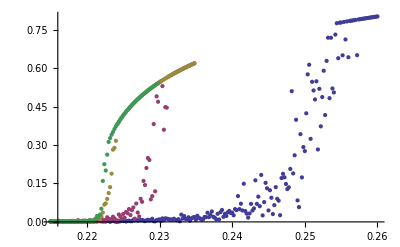

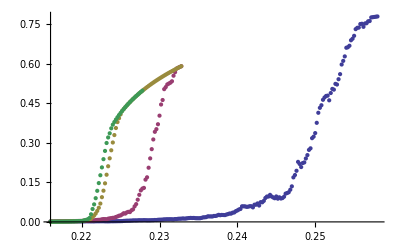

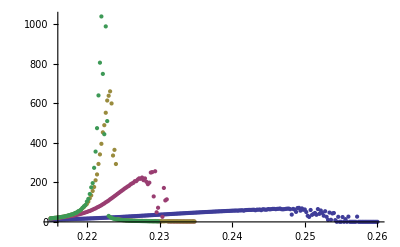

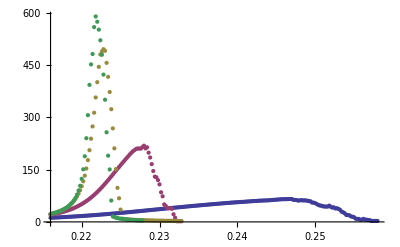

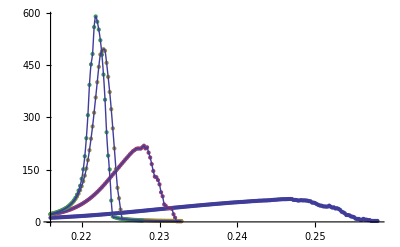

```mathematica
l=8
ListPlot[{m[8],m[16],m[32],m[48]},PlotRange->Full]
ListPlot[{mmod[8],mmod[16],mmod[32],mmod[48]},PlotRange->Full]
ListPlot[{χ[8],χ[16],χ[32],χ[48]},PlotRange->Full]
ListPlot[{χmod[8],χmod[16],χmod[32],χmod[48]},PlotRange->Full]
pic1=ListPlot[{χmod[8],χmod[16],χmod[32],χmod[48]},PlotRange->Full];
Show[{pic1,pic[8],pic[16],pic[32],pic[48]}]
```

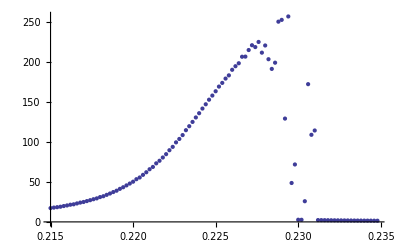

```mathematica
ListPlot[{χ[16]},PlotRange->Full]
```

```mathematica
Do[
ll=ToString[l];
m1[l]=Table[{data1[l][[All,1]][[i]],Abs[data1[l][[All,2]][[i]]]},{i,1,Length[data1[l]]}];
χ1[l]=Table[{data1[l][[All,1]][[i]],data1[l][[All,1]][[i]]*l^3*(data1[l][[All,3]][[i]]-data1[l][[All,2]][[i]]*data1[l][[All,2]][[i]])},{i,1,Length[data1[l]]}];

m2[l]=Table[{data2[l][[All,1]][[i]],Abs[data2[l][[All,2]][[i]]]},{i,1,Length[data2[l]]}];
χ2[l]=Table[{data2[l][[All,1]][[i]],data2[l][[All,1]][[i]]*l^3*(data2[l][[All,3]][[i]]-data2[l][[All,2]][[i]]*data2[l][[All,2]][[i]])},{i,1,Length[data[l]]}];
,{l,{8,16}}]
```

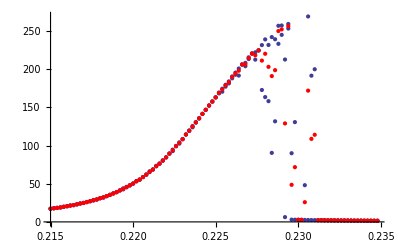

```mathematica
pic1=ListPlot[{χ1[16]},PlotRange->Full];
pic2=ListPlot[{χ2[16]},PlotRange->Full];
pic3=ListPlot[{χ[16]},PlotRange->Full,PlotStyle->{Red,Thick}];
Show[{pic1,pic2,pic3}]
```

```mathematica
l=16;
iχ[l]=Interpolation[χ[l]];
```

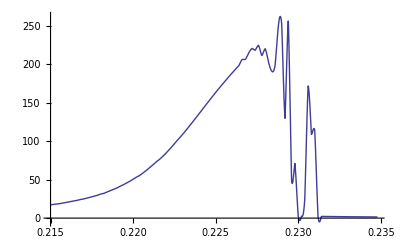

```mathematica
pic4=Plot[iχ[l][x],{x,χ[l][[All,1]][[1]],χ[l][[All,1]][[Length[χ[l]]]]}]
```

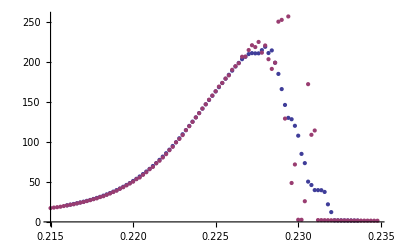

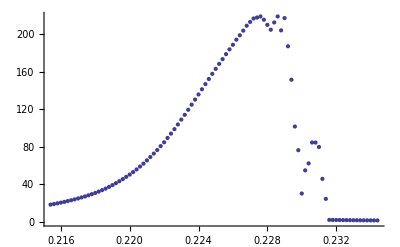

```mathematica
χmod[l]=Table[{χ[l][[All,1]][[i]],(χ[l][[All,2]][[i-5]]+χ[l][[All,2]][[i-4]]+χ[l][[All,2]][[i-3]]+χ[l][[All,2]][[i-2]]+χ[l][[All,2]][[i-1]]+χ[l][[All,2]][[i]]+χ[l][[All,2]][[i+1]]+χ[l][[All,2]][[i+2]]+χ[l][[All,2]][[i+3]]+χ[l][[All,2]][[i+4]]+χ[l][[All,2]][[i+5]])/11.0},{i,6,Length[χ[l]]-6}];
ListPlot[{χmod[l],χ[l]}]
```

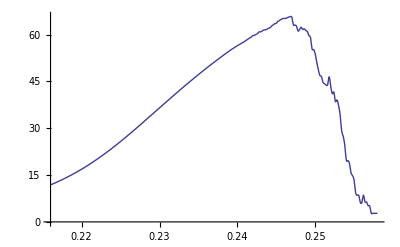

```mathematica
pic4=Plot[{iχmod[l][x],iχmod[16][y]},{x,χmod[l][[All,1]][[1]],χmod[l][[All,1]][[Length[χmod[l]]]]}]
```

```mathematica
------------
```

```mathematica
Do[
ll=ToString[l];
m[l]=Table[{data[l][[All,1]][[i]],Abs[data[l][[All,2]][[i]]]},{i,1,Length[data[l]]}];
χ[l]=Table[{data[l][[All,1]][[i]],data[l][[All,1]][[i]]*l^3*(data[l][[All,3]][[i]]-data[l][[All,2]][[i]]*data[l][[All,2]][[i]])},{i,1,Length[data[l]]}];

χmod[l]=Table[{χ[l][[All,1]][[i]],(χ[l][[All,2]][[i-5]]+χ[l][[All,2]][[i-4]]+χ[l][[All,2]][[i-3]]+χ[l][[All,2]][[i-2]]+χ[l][[All,2]][[i-1]]+χ[l][[All,2]][[i]]+χ[l][[All,2]][[i+1]]+χ[l][[All,2]][[i+2]]+χ[l][[All,2]][[i+3]]+χ[l][[All,2]][[i+4]]+χ[l][[All,2]][[i+5]])/11.0},{i,6,Length[χ[l]]-10}];

mmod[l]=Table[{m[l][[All,1]][[i]],(m[l][[All,2]][[i-5]]+m[l][[All,2]][[i-4]]+m[l][[All,2]][[i-3]]+m[l][[All,2]][[i-2]]+m[l][[All,2]][[i-1]]+m[l][[All,2]][[i]]+m[l][[All,2]][[i+1]]+m[l][[All,2]][[i+2]]+m[l][[All,2]][[i+3]]+m[l][[All,2]][[i+4]]+m[l][[All,2]][[i+5]])/11.0},{i,6,Length[m[l]]-10}];


iχ[l]=Interpolation[χ[l]];
iχmod[l]=Interpolation[χmod[l]];

pic[l]=Plot[{iχmod[l][x]},{x,χmod[l][[All,1]][[1]],χmod[l][[All,1]][[Length[χmod[l]]]]}];

,{l,{8,16,32,48}}]
```

```mathematica
l=8
ListPlot[{m[8],m[16],m[32],m[48]},PlotRange->Full]
ListPlot[{mmod[8],mmod[16],mmod[32],mmod[48]},PlotRange->Full]
ListPlot[{χ[8],χ[16],χ[32],χ[48]},PlotRange->Full]
ListPlot[{χmod[8],χmod[16],χmod[32],χmod[48]},PlotRange->Full]
pic1=ListPlot[{χmod[8],χmod[16],χmod[32],χmod[48]},PlotRange->Full];
Show[{pic1,pic[8],pic[16],pic[32],pic[48]}]
```

8

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

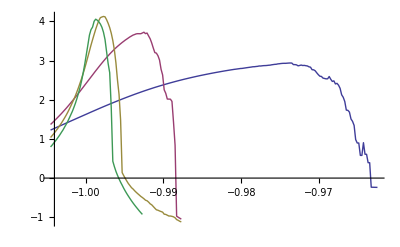

```mathematica
d0=0.2205;
b=1;
z=0;
β=0;
α=-0.6;
Do[
χs[l]=Table[{(χmod[l][[All,1]][[i]]-d0-b*(l)^β)*(l)^z,Log[χmod[l][[All,2]][[i]]]+α*Log[l]},{i,1,Length[χmod[l]]}];
is[l]=Interpolation[χs[l]];
,{l,{8,16,32,48}}
]
pic5=ListLinePlot[{χs[8],χs[16],χs[32],χs[48]},PlotRange->Full]
```

```mathematica
ClearAll[data]
```

```mathematica
l=16;
ll=ToString[l];
hist[l]={}
Do[

ii=ToString[i];
data[i][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EnergyHistogram-l"<>ll<>"-k0.221654-run"<>ii<>".txt",Number];
hist[l]=Join[hist[l],data[i][l]];
,{i,{1,2,3,4,5}}
]
```

{}

```mathematica
l=32;
ll=ToString[l];
hist[l]={}
Do[

ii=ToString[i];
data[i][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EnergyHistogram-l"<>ll<>"-k0.221654-run"<>ii<>".txt",Number];
hist[l]=Join[hist[l],data[i][l]];
,{i,{1,2,3,4}}
]
```

{}

```mathematica
l=48;
ll=ToString[l];
hist[l]={};
Do[

ii=ToString[i];
data[i][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EnergyHistogram-l"<>ll<>"-k0.221654-run"<>ii<>".txt",Number];
hist[l]=Join[hist[l],data[i][l]];
,{i,{1,2,3,4}}
]
```

```mathematica
l=64;
ll=ToString[l];
hist[l]={}
Do[

ii=ToString[i];
data[i][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EnergyHistogram-l"<>ll<>"-k0.221654-run"<>ii<>".txt",Number];
hist[l]=Join[hist[l],data[i][l]];
,{i,{1,2,3,4,5,6,7,8}}
]
```

{}

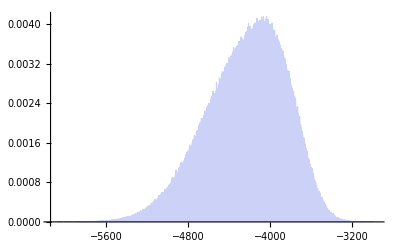

```mathematica
Histogram[data[1][16],{4},"Probability"]
```

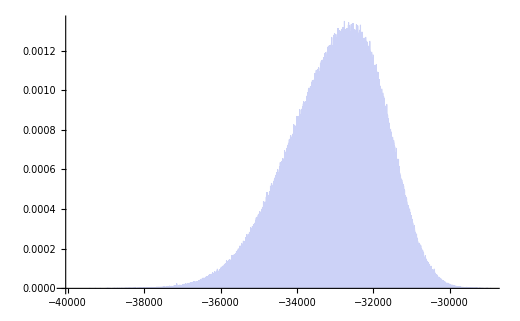

```mathematica
Histogram[hist[32],{4},"Probability"]
```

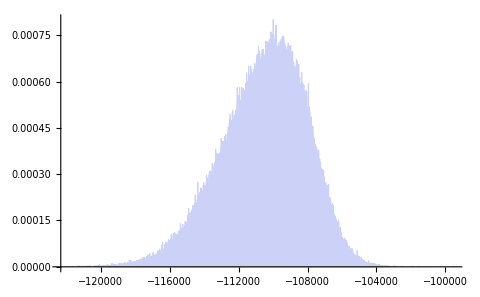

```mathematica
Histogram[hist[48],{4},"Probability"]
```

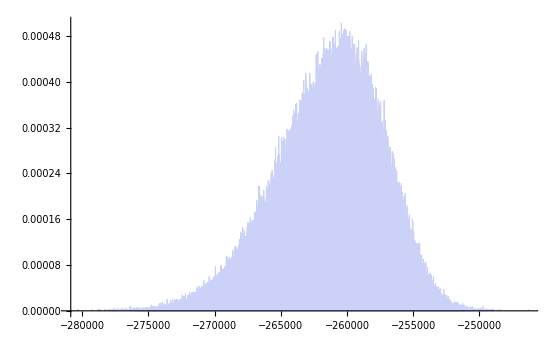

```mathematica
Histogram[hist[64],{4},"Probability"]
```

```mathematica
ClearAll[pdf]
```

```mathematica
l=32;
pdf[l]=HistogramDistribution[hist[l],{4}];
```

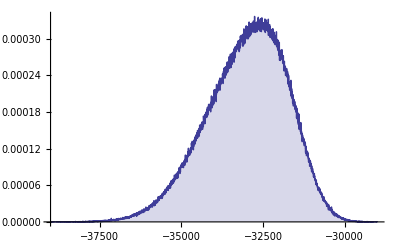

```mathematica
DiscretePlot[PDF[pdf[l],x],{x,-39000,-29000,1},PlotRange->Full]
```

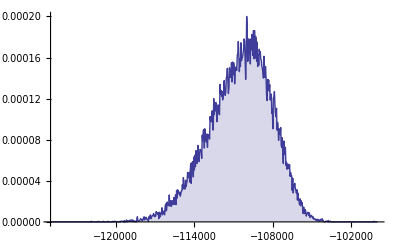

```mathematica
l=48;
pdf[l]=HistogramDistribution[hist[l],{4}];
DiscretePlot[PDF[pdf[l],x],{x,-125000,-100000,40},PlotRange->Full]
```

```mathematica
{g,{binCounts}}=Reap[Histogram[hist,{-6500,-2500,4},Function[{bins,counts},Sow[counts]]]];
```

```mathematica
{g,ListLinePlot[binCounts]}
```

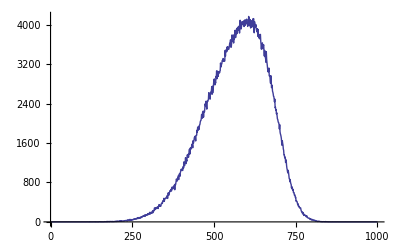

```mathematica
ListLinePlot[binCounts,PlotRange->Full]
```

```mathematica
l=16;
ll=ToString[l];
hist[l]={}
Do[

ii=ToString[i];
data[i][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EnergyHistogram-l"<>ll<>"-k0.221654-run"<>ii<>".txt",Number];
hist[l]=Join[hist[l],data[i][l]];
,{i,{1,2,3,4,5}}
]
```

```mathematica
l=16;
ll=ToString[l];
Do[
dd=ToString[d];
histd[d][l]={};
Do[

ii=ToString[i];
data[i][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/Ising/ising-EnergyHistogram-l"<>ll<>"-k"<>dd<>"-run"<>ii<>".txt",Number];
histd[d][l]=Join[histd[d][l],data[i][l]];
,{i,{1,2,3,4,5}}
]
,{d,{0.21,0.214,0.218,0.222,0.226,0.23,0.234}}
]
```

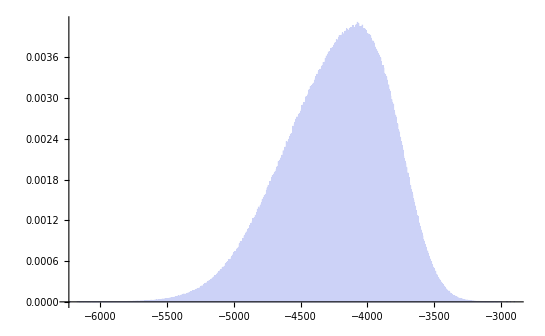

```mathematica
Histogram[hist[16],{4},"Probability"]
```

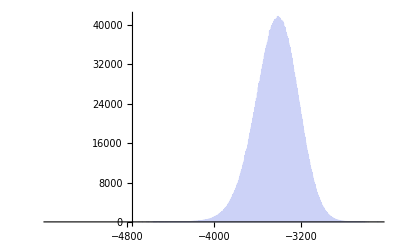

```mathematica
Histogram[histd[0.21][16],{4},PlotRange->{{-5500,-2500},Full}]
```

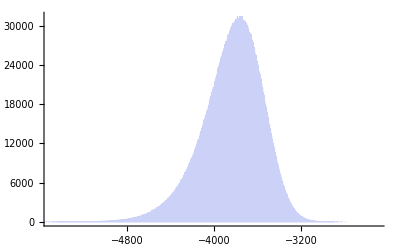

```mathematica
Histogram[histd[0.218][16],{4},PlotRange->{{-5500,-2500},Full}]
```

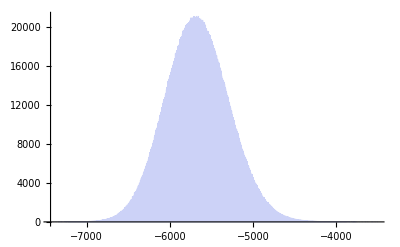

```mathematica
Histogram[histd[0.23][16],{4}]
```

```mathematica
l=16;
d=0.23;
pdf[l]=HistogramDistribution[hist[l],{4}];
```

```mathematica
l=16;
d=0.23;
pdfd[d][l]=HistogramDistribution[histd[d][l],{4}];
```

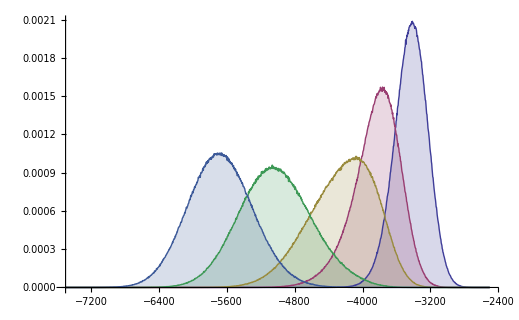

```mathematica
DiscretePlot[{PDF[pdfd[0.21][l],x],PDF[pdfd[0.218][l],x],PDF[pdf[l],x],PDF[pdfd[0.226][l],x],PDF[pdfd[0.23][l],x]},{x,-7500,-2500,4},PlotRange->Full]
```

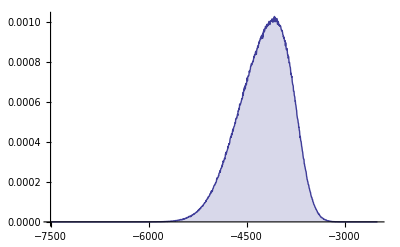

```mathematica
DiscretePlot[{PDF[pdf[l],x]},{x,-7500,-2500,4},PlotRange->Full]
```